```mathematica
Quiet@Remove["Global`*"];
```

```mathematica
f = 50;
ω= 2.Pi*f;
T = 1/f;
U[t_]:= 10 *Sin[ω*t]+ Sin[3*ω*t]+ 0.5*Sin[5*ω*t];
Plot[U[t], {t, 0, 3T}];
rn := 1.8*RandomReal[{-1, 1}];
datawithNoise = Table[{t, U[t]+rn}, {t, 0., 3T, T/150}];
ListPlot[datawithNoise];
Export["data.csv", datawithNoise]
```

data.csv

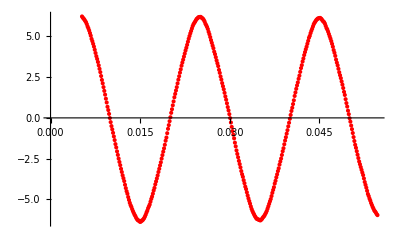

```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["data.csv"];
ListPlot[data];
filteredData =MovingAverage[data, 80]
ListPlot[MovingAverage[data, 80], PlotStyle->Red]
```

```mathematica
intData = Interpolation[filteredData];
t1 = t/.FindRoot[intData[t] == 0, {t, 0.01}]
t2 = t/.FindRoot[intData[t] == 0, {t, 0.02}]
t3 = t/.FindRoot[intData[t] == 0, {t, 0.03}]
t4 = t/.FindRoot[intData[t] == 0, {t, 0.04}]
t5 = t/.FindRoot[intData[t] == 0, {t, 0.05}]
periods = {t3-t1, t4-t2, t5-t3};
Tint = Mean[periods]
```

Interpolation::innd: First argument in filteredData does not contain a list of data and coordinates.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.01]} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.01]} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.FindRoot[intData[t]==0,{t,0.01}]

FindRoot::nlnum: The function value {Interpolation[filteredData][0.02]} is not a list of numbers with dimensions {1} at {t} = {0.02}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.02}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.02]} is not a list of numbers with dimensions {1} at {t} = {0.02}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.02}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.FindRoot[intData[t]==0,{t,0.02}]

FindRoot::nlnum: The function value {Interpolation[filteredData][0.03]} is not a list of numbers with dimensions {1} at {t} = {0.03}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.03}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.03]} is not a list of numbers with dimensions {1} at {t} = {0.03}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.03}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.FindRoot[intData[t]==0,{t,0.03}]

FindRoot::nlnum: The function value {Interpolation[filteredData][0.04]} is not a list of numbers with dimensions {1} at {t} = {0.04}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.04}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.04]} is not a list of numbers with dimensions {1} at {t} = {0.04}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.04}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.FindRoot[intData[t]==0,{t,0.04}]

FindRoot::nlnum: The function value {Interpolation[filteredData][0.05]} is not a list of numbers with dimensions {1} at {t} = {0.05}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.05}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.05]} is not a list of numbers with dimensions {1} at {t} = {0.05}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.05}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.FindRoot[intData[t]==0,{t,0.05}]

FindRoot::nlnum: The function value {Interpolation[filteredData][0.03]} is not a list of numbers with dimensions {1} at {t} = {0.03}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.03}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.01]} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.04]} is not a list of numbers with dimensions {1} at {t} = {0.04}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.04}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.01]} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.03]} is not a list of numbers with dimensions {1} at {t} = {0.03}.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.03}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Interpolation[filteredData][0.02]} is not a list of numbers with dimensions {1} at {t} = {0.02}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[intData[t]==0,{t,0.02}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

1/3 (-(t/.FindRoot[intData[t]==0,{t,0.01}])-(t/.FindRoot[intData[t]==0,{t,0.02}])+(t/.FindRoot[intData[t]==0,{t,0.04}])+(t/.FindRoot[intData[t]==0,{t,0.05}]))

```mathematica
dat2 = Partition[filteredData, 2, 1];
test[{{t1_,u1_}, {t2_, u2_}}] := u1*u2<0;
selData = Select[dat2, test]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

Partition[]